```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY197/sec_int_data/778nm.dat"]
```

{{1.50189,-0.0177364},{1.45414,-0.0335981},{1.33983,-0.0191624},{1.30748,-0.0202027},{1.27821,-0.0239137},{1.24682,-0.0568032},{1.22351,-0.206385},{1.20659,-0.335669},{1.18213,-0.617854},{1.16419,-0.834826},{1.15263,-0.998423},{1.13304,-1.2504},{1.09662,-0.176558},{1.09807,-0.247244},{1.10207,-0.269777},{1.10747,-0.245977},{1.11401,-0.233889},{1.12685,-0.208698},{1.13867,-0.17933},{1.15401,-0.169532},{1.16573,-0.159547},{1.20258,-0.165689},{1.26466,-0.148048},{1.30748,-0.152231},{1.33983,-0.163637},{1.37936,-0.167945}}

-1.71883+1.18242 x

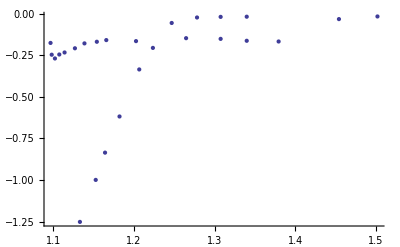

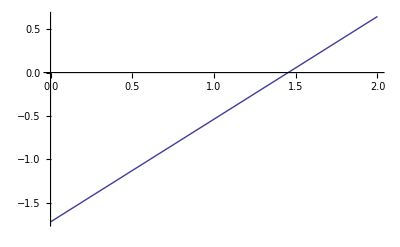

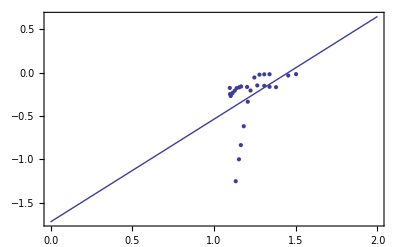

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```